```mathematica
Notation`AutoLoadNotationPalette=False;
Internal`InheritedBlock[{SetDelayed},Unprotect@SetDelayed;
HoldPattern[Notation`AddInputAlias[args___]:=With[v:{s_=_,o_=_},With[_,SetOptions[n_,InputAliases->Join[_,_]]]]]:=(Notation`AddInputAlias[args]:=With[v,SetOptions[n,InputAliases->Join[o,<|s|>]]]);
Quiet[<<Notation`]]
```

```mathematica
SetOptions[$FrontEnd,InputAliases->FirstCase[Quiet@CurrentValue[$FrontEnd,InputAliases],_Association,Inherited,All]]
Symbolize[ParsedBoxWrapper[SubscriptBox["_","_"]]]
Symbolize[ParsedBoxWrapper[OverscriptBox["_","_"]]]
```

### Kerr geometry in Boyer-Lindquist coordinates

```mathematica
<<EDCRGTCcode`
Unprotect[metric];
$Assumptions={0≤a≤M,0≤r^2+a^2-2M r,0≤r,0≤θ≤π,0≤ϕ<2π};
coord={t,r,θ,ϕ};
Clear[Δ,Σ,Π]
metric=({{-(1-(2M r)/Σ[r,θ]), 0, 0, -(2 a M r)/Σ[r,θ] Sin[θ]^2}, {0, Σ[r,θ]/Δ[r], 0, 0}, {0, 0, Σ[r,θ], 0}, {-(2 a M r)/Σ[r,θ] Sin[θ]^2, 0, 0, Π[r,θ]/Σ[r,θ] Sin[θ]^2}})//FullSimplify;
d[M]=0;d[a]=0;
RGtensors[metric,coord,{1,0,0}]
```

SetDelayed::write: Tag Classify in Classify[x_] is Protected.

gdd = (-1+(2 M r)/Σ[r,θ] | 0 | 0 | -(2 a M r Sin[θ]^2)/Σ[r,θ]
0 | Σ[r,θ]/Δ[r] | 0 | 0
0 | 0 | Σ[r,θ] | 0
-(2 a M r Sin[θ]^2)/Σ[r,θ] | 0 | 0 | (Sin[θ]^2 Π[r,θ])/Σ[r,θ])

LineElement = -(4 a M r d[t] d[ϕ] Sin[θ]^2)/Σ[r,θ]+(d[ϕ]^2 Sin[θ]^2 Π[r,θ])/Σ[r,θ]+(d[t]^2 (2 M r-Σ[r,θ]))/Σ[r,θ]+d[θ]^2 Σ[r,θ]+(d[r]^2 Σ[r,θ])/Δ[r]

gUU = (-(Π[r,θ] Σ[r,θ])/(4 a^2 M^2 r^2 Sin[θ]^2-2 M r Π[r,θ]+Π[r,θ] Σ[r,θ]) | 0 | 0 | -(2 a M r Σ[r,θ])/(4 a^2 M^2 r^2 Sin[θ]^2-2 M r Π[r,θ]+Π[r,θ] Σ[r,θ])
0 | Δ[r]/Σ[r,θ] | 0 | 0
0 | 0 | 1/Σ[r,θ] | 0
-(2 a M r Σ[r,θ])/(4 a^2 M^2 r^2 Sin[θ]^2-2 M r Π[r,θ]+Π[r,θ] Σ[r,θ]) | 0 | 0 | (Csc[θ]^4 (2 M r-Σ[r,θ]) Σ[r,θ])/(-4 a^2 M^2 r^2+2 M r Csc[θ]^2 Π[r,θ]-Csc[θ]^2 Π[r,θ] Σ[r,θ]))

gUU computed in 0.013789 sec

Gamma computed in 0.012763 sec

Riemann(dddd) computed in 0.04335 sec

Riemann(Uddd) computed in 0.157492 sec

Ricci computed in 0.119279 sec

Weyl tensor not computed

Einstein tensor not computed

All tasks completed in 0.352395 seconds

```mathematica
Δ[r_]:=r^2+a^2-2M r;
Σ[r_,θ_]:=r^2+a^2 Cos[θ]^2;
Π[r_,θ_]:=(r^2+a^2)^2-a^2 Δ[r] Sin[θ]^2;
R//Simplify
Clear[R]
```

0

```mathematica
inducedLineElement=LineElement/.{θ->π/2,d[θ]->0,d[t]->0};

(* We seek functions Z and R such that the embedding metric matches the induced geometry *)
d[Z]^2+d[R]^2+R^2 d[ϕ]^2/.{R->R[r],Z->Z[r]}//Simplify ;
inducedLineElement==%/.R->Function[r,(√((r^2+a^2)^2-a^2 Δ[r]))/r]/.Z'[r]->√(r^2/Δ[r]-(D[√(((r^2+a^2)^2-a^2 Δ[r])/r^2), r])^2)//Simplify
```

True

### Schwarzschild

```mathematica
√(r^2/Δ[r]-(D[√(((r^2+a^2)^2-a^2 Δ[r])/r^2), r])^2)/.a->0;
Simplify[{(√((r^2+a^2)^2-a^2 Δ[r]))/r,Integrate[%,r]}/.a->0,r>2M>0]
```

{r,2 M √(-4+(2 r)/M)}

```mathematica
Z[R_]:=2 M √(-4+(2 R)/M);
Block[{M=1},
RevolutionPlot3D[Z[R],{R,2M,10M}]]
```

-Graphics3D-

### Kerr

```mathematica
Series[(√((r^2+a^2)^2-a^2 Δ[r]))/r,{r,∞,4}]
```

r+a^2/(2 r)+(a^2 M)/r^2-a^4/(8 r^3)-(a^4 M)/(2 r^4)+O[1/r]^5

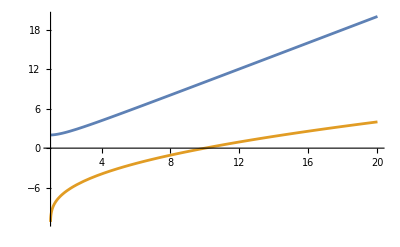

```mathematica
Block[{M=1,a=999/1000,rH=M+√(M^2-a^2)},
embedding=Plot[{(√((r^2+a^2)^2-a^2 Δ[r]))/r,NIntegrate[√(s^2/Δ[s]-(D[√(((s^2+a^2)^2-a^2 Δ[s])/s^2), s])^2),{s,10,r}]//Re},{r,rH,20},Exclusions->None]]
Rofr=Cases[embedding,x_Line:>First@x,∞][[1]];
Zofr=Cases[embedding,x_Line:>First@x,∞][[2]];
```

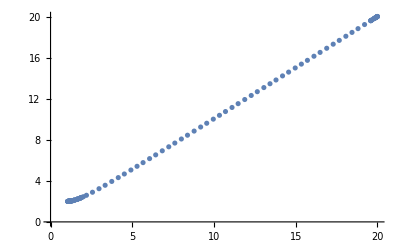

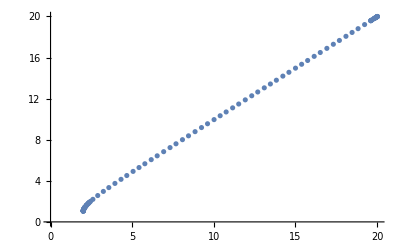

```mathematica
ListPlot@Rofr
rofR=Map[Reverse[#]&,Rofr];
ListPlot@rofR
```

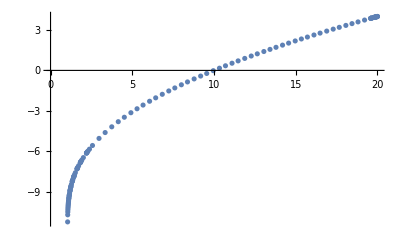

```mathematica
ListPlot@Zofr
Zn[r_]:=Interpolation[Zofr][r]
Rn[r_]:=Interpolation[Rofr][r]
rn[R_]:=Interpolation[rofR][R]
```

```mathematica
SetDirectory@NotebookDirectory[];
Import["./trajectories/equatorial-rays/ray1.csv","CSV"];
trajectory=(1/10)%;
sphericalTrajectory=ParallelMap[CoordinateTransform["Cartesian"->"Spherical",#]&,trajectory];
cylindricalTrajectory=ParallelMap[{Rn[#[[1]]],#[[3]],Zn[#[[1]]]}&,%];
embeddedCartesianTrajectory=ParallelMap[CoordinateTransform["Cylindrical"->"Cartesian",#]&,%];
Export["./trajectories/embeddingDiagram/ray1.csv",embeddedCartesianTrajectory]
```

```mathematica
(* Camera's parametric trajectory *)
frameRate=40.0; 
tMax=90.0;
Δt=tMax/(frameRate*tMax);
yend=7;
xCam[t_]:=0;
yCam[t_]:=yend*(t/tMax)^3;
zCam[t_,z0_]:=(3yCam[t])^0.8+z0;
cameraTrajectory=Table[{xCam[t],yCam[t],zCam[t,-7]},{t,0,tMax,Δt}];
Export["./trajectories/embeddingDiagram/cameraTrajectory.csv",cameraTrajectory]
```

./trajectories/embeddingDiagram/cameraTrajectory.csv

```mathematica
M=1;
a=999/1000;
rH=M+√(M^2-a^2);
RH=Interpolation[Rofr][rH];
Manipulate[Show[
RevolutionPlot3D[Zn[rn[R]],{R,RH,10},PlotRange->{{-10,10},{-10,10},{-15,2}}],
ListLinePlot3D[embeddedCartesianTrajectory[[1;;i]]],
ListLinePlot3D[cameraTrajectory[[1;;i]]]
],{i,1,3600}]
```

./trajectories/embeddingDiagram/ray1.csv

```mathematica
SetDirectory@NotebookDirectory[];
Block[{M=1,a=999/1000,rH=M+√(M^2-a^2),RH},
RH=Interpolation[Rofr][rH];
surface=RevolutionPlot3D[Zn[rn[R]],{R,RH,7},PlotPoints->500,MaxRecursion->4];
(*Export the surface to an OBJ file*)
Export["./models/surface.obj",surface];
]
```

$Aborted

```mathematica
Show[surface]
```

-Graphics3D-

```mathematica
Block[{M=1,a=999/1000,rH=M+√(M^2-a^2),RH},
RH=Interpolation[Rofr][rH];
surface=RevolutionPlot3D[Zn[rn[R]],{R,RH,7},PlotPoints->100,MaxRecursion->4]
]
```

-Graphics3D-

```mathematica
Export["./models/surface.obj",surface];
```